```mathematica
$Assumptions={n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals}
```

{n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals}

```mathematica
HFunc[AA_,BB_,CC_,DD_,EE_,FF_,YY_,y_,t_]:= (FF (1/2 DD ⅇ^((EE y)/(1+CC t^2)) t (y-YY)+1/2 DD ⅇ^(-(EE y)/(1+CC t^2)) t (y+YY)+DD t y Cos[(BB t y)/(1+CC t^2)]-AA  Sin[(BB t y)/(1+CC t^2)]))/((1+CC t^2) (ⅇ^(-(EE y)/(1+CC t^2))+ⅇ^((EE y)/(1+CC t^2))+2 Cos[(BB t y)/(1+CC t^2)]))
```

```mathematica
Hollandtabl=Table[NDSolve[{y'[t]==(HFunc[1,10,0.50,1,10,1,10,y[t],t]),y[0]==(8+i/20)},y,{t,0,30}],{i,100}];
```

```mathematica
Hollandtabl2=Table[NDSolve[{y'[t]==(HFunc[1,10,0.50,1,10,1,10,y[t],t]),y[0]==-(8+i/20)},y,{t,0,30}],{i,100}];
```

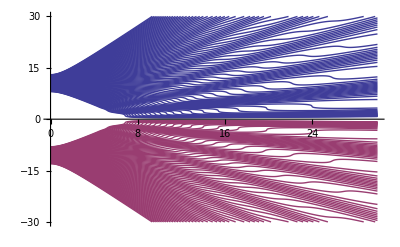

```mathematica
Plot[{(Evaluate[y[t]/.Hollandtabl]),(Evaluate[y[t]/.Hollandtabl2])},{t,0,30},PlotRange->{Full,{-30,30}}]
```

```mathematica
QuantPot[AA_,BB_,CC_,DD_,EE_,FF_,YY_,y_,t_] := D[D[Abs[HFunc[AA,BB,CC,DD,EE,FF,YY,y,t]], t], y] / Abs[HFunc[AA,BB,CC,DD,EE,FF,YY,y,t]]
```

```mathematica
Simplify[QuantPot[AA,BB,CC,DD,EE,FF,YY,y,t]]
```

$Aborted

```mathematica
Hollandtabl3=Table[NDSolve[{y'[t]==(HFunc2[1,10,1,1,1,2,y[t],t]),y[0]==(1+i/50)},y,{t,0,5}],{i,100}];
```

```mathematica
ⅇ^(ⅈ (x-d) p -ⅈ p^2 t)+ⅇ^(ⅈ (x+d) p -ⅈ p^2 t)
```

ⅇ^(-ⅈ p^2 t+ⅈ p (-d+x))+ⅇ^(-ⅈ p^2 t+ⅈ p (d+x))

```mathematica
Integrate[ⅇ^(-ⅈ p^2 t+ⅈ p (-d+x))+ⅇ^(-ⅈ p^2 t+ⅈ p (d+x)),{x,-w,w}]
```

(4 ⅇ^(-ⅈ p^2 t) Cos[d p] Sin[p w])/p

```mathematica
Integrate[(Cos[d p] Sin[p w])/p ⅇ^(-ⅈ p^2 t+ⅈ p x),{p,-∞,∞}]
```

$Aborted

```mathematica
Integrate[(π/a)^(-1)Sinc[a (x -t)]^2,{x,-∞,∞}]
```

1

```mathematica
Integrate[Sin[p w]/p ⅇ^(-ⅈ p^2 t+ⅈ p x),{p,-∞,∞}]
```

(1/2-ⅈ/2) π (FresnelC[(w-x)/(√(2 π) √t)]+FresnelC[(w+x)/(√(2 π) √t)]+ⅈ (FresnelS[(w-x)/(√(2 π) √t)]+FresnelS[(w+x)/(√(2 π) √t)]))

```mathematica
FullSimplify[(1/2-ⅈ/2) π (FresnelC[(w-x)/(√(2 π) √t)]+FresnelC[(w+x)/(√(2 π) √t)]+ⅈ (FresnelS[(w-x)/(√(2 π) √t)]+FresnelS[(w+x)/(√(2 π) √t)]))(1/2+ⅈ/2) π (FresnelC[(w-x)/(√(2 π) √t)]+FresnelC[(w+x)/(√(2 π) √t)]-ⅈ (FresnelS[(w-x)/(√(2 π) √t)]+FresnelS[(w+x)/(√(2 π) √t)]))]
```

1/2 π^2 ((FresnelC[(w-x)/(√(2 π) √t)]+FresnelC[(w+x)/(√(2 π) √t)])^2+(FresnelS[(w-x)/(√(2 π) √t)]+FresnelS[(w+x)/(√(2 π) √t)])^2)

```mathematica
ψ = (2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) σ)^(-1/2)(ⅇ^((-(d+x)^2)/(4 σ^2)) + ⅇ^((-(d-x)^2)/(4 σ^2)))ⅇ^(ⅈ x t)
```

(ⅇ^(ⅈ t x) (ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2))))/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ))

```mathematica
Integrate[(ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2)))/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ))(ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2)))/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ)),{x,-∞,∞}]
```

1

```mathematica
Integrate[(ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2)))/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ))ⅇ^(-ⅈ x p),{x,-∞,∞}]
```

(ⅇ^(-p (ⅈ d+p σ^2)) (1+ⅇ^(2 ⅈ d p)) (2 π)^(1/4) σ)/(√((1+ⅇ^(-d^2/(2 σ^2))) σ))

```mathematica
Integrate[(ⅇ^(-p (ⅈ d+p σ^2)) (1+ⅇ^(2 ⅈ d p)) (2 π)^(1/4) σ)/(√((1+ⅇ^(-d^2/(2 σ^2))) σ))ⅇ^(ⅈ x p + ⅈ p^2 t),{p,-∞,∞}]
```

```mathematica
(4 π^2)^(-1/2)(2^(1/4) (ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) π^(3/4) σ)/(√((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2)))
```

((ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2)))

```mathematica
Integrate[((ⅇ^(-(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (ⅈ t+σ^2)))((ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2))),{x,-∞,∞}]
```

1

```mathematica
FullSimplify[Sqrt[((ⅇ^(-(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (ⅈ t+σ^2)))((ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2)))]]
```

```mathematica
FullSimplify[((ⅇ^(-(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (ⅈ t+σ^2)))((ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2)))]
```

(ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) (ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2)))) (ⅇ^((d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^((d+x)^2/(4 (ⅈ t+σ^2)))) σ)/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4))

```mathematica
(ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2)))ⅇ^((d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^((d-x)^2/(4 (ⅈ t+σ^2)))ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^((d+x)^2/(4 (ⅈ t+σ^2)))ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^((d+x)^2/(4 (ⅈ t+σ^2)))ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2))))
```

ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2))+(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2))+(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2))+(d+x)^2/(4 (ⅈ t+σ^2)))+ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2))+(d+x)^2/(4 (ⅈ t+σ^2)))

```mathematica
FullSimplify[ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2))+(d-x)^2/(4 (ⅈ t+σ^2)))] + FullSimplify[ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2))+(d-x)^2/(4 (ⅈ t+σ^2)))] + FullSimplify[ⅇ^((d-x)^2/(4 (-ⅈ t+σ^2))+(d+x)^2/(4 (ⅈ t+σ^2)))] + FullSimplify[ⅇ^((d+x)^2/(4 (-ⅈ t+σ^2))+(d+x)^2/(4 (ⅈ t+σ^2)))]
```

```mathematica
ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4)))(ⅇ^((-2 ⅈ d t x)/(2 (t^2+σ^4)))+ⅇ^((2 ⅈ d t x)/(2 (t^2+σ^4))))
```

```mathematica
ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) (2 Cos[(d t x)/(t^2+σ^4)])
```

ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]

```mathematica
(ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]) σ)/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4))
```

(ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4))

```mathematica
FullSimplify[((ⅇ^(-(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (ⅈ t+σ^2)))D[((ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2))),x]-((ⅇ^(-(d-x)^2/(4 (-ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (-ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (-ⅈ t+σ^2)))D[((ⅇ^(-(d-x)^2/(4 (ⅈ t+σ^2)))+ⅇ^(-(d+x)^2/(4 (ⅈ t+σ^2)))) σ)/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ (ⅈ t+σ^2))),x]]
```

-(ⅇ^((d^2 t^2-2 ⅈ d t x σ^2-(d^2+2 x^2) σ^4)/(2 σ^2 (t^2+σ^4))) σ (-ⅈ ⅇ^((ⅈ d t x)/(t^2+σ^4)) t (ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4))) (d-x)-ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4))) (d+x))+ⅈ ⅇ^((4 ⅈ d t x+(d^2+x^2) σ^2)/(2 (t^2+σ^4))) (t x+ⅈ d σ^2)+ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) (ⅈ t x+d σ^2)))/(2 (1+ⅇ^(d^2/(2 σ^2))) √(2 π) (t^2+σ^4)^(3/2))

```mathematica
FullSimplify[(-(ⅇ^((d^2 t^2-2 ⅈ d t x σ^2-(d^2+2 x^2) σ^4)/(2 σ^2 (t^2+σ^4))) σ (-ⅈ ⅇ^((ⅈ d t x)/(t^2+σ^4)) t (ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4))) (d-x)-ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4))) (d+x))+ⅈ ⅇ^((4 ⅈ d t x+(d^2+x^2) σ^2)/(2 (t^2+σ^4))) (t x+ⅈ d σ^2)+ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) (ⅈ t x+d σ^2)))/(2 (1+ⅇ^(d^2/(2 σ^2))) √(2 π) (t^2+σ^4)^(3/2)))/Sqrt[(ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4))]]
```

(ⅈ ⅇ^(d^2/(4 σ^2)) (2/π)^(1/4) (-t x Cos[(d t x)/(t^2+σ^4)]-t x Cosh[(d x σ^2)/(t^2+σ^4)]+d σ^2 Sin[(d t x)/(t^2+σ^4)]+d t Sinh[(d x σ^2)/(t^2+σ^4)]))/((t^2+σ^4)^(5/4) √(((1+ⅇ^(d^2/(2 σ^2))) (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/σ))

```mathematica
FullSimplify[(-(ⅇ^((d^2 t^2-2 ⅈ d t x σ^2-(d^2+2 x^2) σ^4)/(2 σ^2 (t^2+σ^4))) σ (-ⅈ ⅇ^((ⅈ d t x)/(t^2+σ^4)) t (ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4))) (d-x)-ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4))) (d+x))+ⅈ ⅇ^((4 ⅈ d t x+(d^2+x^2) σ^2)/(2 (t^2+σ^4))) (t x+ⅈ d σ^2)+ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) (ⅈ t x+d σ^2)))/(2 (1+ⅇ^(d^2/(2 σ^2))) √(2 π) (t^2+σ^4)^(3/2)))/((ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4)))]
```

-(ⅈ (t x Cos[(d t x)/(t^2+σ^4)]+t x Cosh[(d x σ^2)/(t^2+σ^4)]-d σ^2 Sin[(d t x)/(t^2+σ^4)]-d t Sinh[(d x σ^2)/(t^2+σ^4)]))/((t^2+σ^4) (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]))

```mathematica
FullSimplify[1/((ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4)))]
```

(2 ⅇ^(-(d^2-(2 (d^2+x^2) σ^4)/(t^2+σ^4))/(4 σ^2)) √(2 π) √(t^2+σ^4) Cosh[d^2/(4 σ^2)])/(σ (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]))

```mathematica
VelocityField[d_, σ_, x_, t_]:=-(t x Cos[(d t x)/(t^2+σ^4)]+t x Cosh[(d x σ^2)/(t^2+σ^4)]-d σ^2 Sin[(d t x)/(t^2+σ^4)]-d t Sinh[(d x σ^2)/(t^2+σ^4)])/((t^2+σ^4) (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]))
```

```mathematica
FullSimplify[D[VelocityField[d, σ, x, t],t]]
```

(2 x (t^4-3 d^2 t^2 σ^2+(d-σ) σ^6 (d+σ))+x (t^4-σ^8) Cos[(2 d t x)/(t^2+σ^4)]-2 d t σ^2 (t^2+σ^4) Sin[(2 d t x)/(t^2+σ^4)]+2 d t Sin[(d t x)/(t^2+σ^4)] (-2 σ^2 (t^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]-d x (t^2-3 σ^4) Sinh[(d x σ^2)/(t^2+σ^4)])+2 Cos[(d t x)/(t^2+σ^4)] (x (2 t^4-3 d^2 t^2 σ^2+d^2 σ^6-2 σ^8) Cosh[(d x σ^2)/(t^2+σ^4)]+d (-t^4+σ^8) Sinh[(d x σ^2)/(t^2+σ^4)])+(t^4-σ^8) (x Cosh[(2 d x σ^2)/(t^2+σ^4)]-d Sinh[(2 d x σ^2)/(t^2+σ^4)]))/(2 (t^2+σ^4)^3 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])^2)

```mathematica
Simplify[D[D[√f[x],x],x]]
```

(-f'[x]^2+2 f[x] f''[x])/(4 f[x]^(3/2))

```mathematica
FullSimplify[(1/2)D[D[(ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4)),x],x](ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4))]
```

-(ⅇ^((d^2 t^2-x^2 σ^4)/(t^2 σ^2+σ^6)) σ^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]) ((d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 ((t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (-t Sin[(d t x)/(t^2+σ^4)]+σ^2 Sinh[(d x σ^2)/(t^2+σ^4)]))))/(4 (1+ⅇ^(d^2/(2 σ^2)))^2 π (t^2+σ^4)^3)

```mathematica
FullSimplify[D[(ⅇ^(-((d^2+x^2) σ^2)/(t^2+σ^4)) σ (ⅇ^(((d-x)^2 σ^2)/(2 (t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (t^2+σ^4)))+2 ⅇ^(((d^2+x^2) σ^2)/(2 (t^2+σ^4))) Cos[(d t x)/(t^2+σ^4)]))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(t^2+σ^4)),x]]
```

-(ⅇ^((d^2 t^2-x^2 σ^4)/(2 t^2 σ^2+2 σ^6)) σ (x σ^2 Cos[(d t x)/(t^2+σ^4)]+d t Sin[(d t x)/(t^2+σ^4)]+σ^2 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)])))/((1+ⅇ^(d^2/(2 σ^2))) √(2 π) (t^2+σ^4)^(3/2))

```mathematica
FullSimplify[-(1/4)(-(ⅇ^((d^2 t^2-x^2 σ^4)/(2 t^2 σ^2+2 σ^6)) σ (x σ^2 Cos[(d t x)/(t^2+σ^4)]+d t Sin[(d t x)/(t^2+σ^4)]+σ^2 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)])))/((1+ⅇ^(d^2/(2 σ^2))) √(2 π) (t^2+σ^4)^(3/2)))^2]
```

-(ⅇ^((d^2 t^2-x^2 σ^4)/(t^2 σ^2+σ^6)) (x σ^3 Cos[(d t x)/(t^2+σ^4)]+d t σ Sin[(d t x)/(t^2+σ^4)]+σ^3 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2)/(8 (1+ⅇ^(d^2/(2 σ^2)))^2 π (t^2+σ^4)^3)

```mathematica
FullSimplify[(-(ⅇ^((d^2 t^2-x^2 σ^4)/(t^2 σ^2+σ^6)) σ^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]) ((d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 ((t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (-t Sin[(d t x)/(t^2+σ^4)]+σ^2 Sinh[(d x σ^2)/(t^2+σ^4)]))))/(4 (1+ⅇ^(d^2/(2 σ^2)))^2 π (t^2+σ^4)^3))+(-(ⅇ^((d^2 t^2-x^2 σ^4)/(t^2 σ^2+σ^6)) (x σ^3 Cos[(d t x)/(t^2+σ^4)]+d t σ Sin[(d t x)/(t^2+σ^4)]+σ^3 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2)/(8 (1+ⅇ^(d^2/(2 σ^2)))^2 π (t^2+σ^4)^3))]
```

(ⅇ^((d^2 t^2-x^2 σ^4)/(t^2 σ^2+σ^6)) (-(x σ^3 Cos[(d t x)/(t^2+σ^4)]+d t σ Sin[(d t x)/(t^2+σ^4)]+σ^3 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2-2 σ^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]) ((d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 ((t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (-t Sin[(d t x)/(t^2+σ^4)]+σ^2 Sinh[(d x σ^2)/(t^2+σ^4)])))))/(8 (1+ⅇ^(d^2/(2 σ^2)))^2 π (t^2+σ^4)^3)

```mathematica
FullSimplify[((2 ⅇ^(-(d^2-(2 (d^2+x^2) σ^4)/(t^2+σ^4))/(4 σ^2)) √(2 π) √(t^2+σ^4) Cosh[d^2/(4 σ^2)])/(σ (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])))^2((ⅇ^((d^2 t^2-x^2 σ^4)/(t^2 σ^2+σ^6)) (-(x σ^3 Cos[(d t x)/(t^2+σ^4)]+d t σ Sin[(d t x)/(t^2+σ^4)]+σ^3 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2-2 σ^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]) ((d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 ((t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (-t Sin[(d t x)/(t^2+σ^4)]+σ^2 Sinh[(d x σ^2)/(t^2+σ^4)])))))/(8 (1+ⅇ^(d^2/(2 σ^2)))^2 π (t^2+σ^4)^3))]
```

(ⅇ^(d^2/(2 σ^2)) Cosh[d^2/(4 σ^2)]^2 (-(x σ^3 Cos[(d t x)/(t^2+σ^4)]+d t σ Sin[(d t x)/(t^2+σ^4)]+σ^3 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2-2 σ^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]) ((d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 ((t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (-t Sin[(d t x)/(t^2+σ^4)]+σ^2 Sinh[(d x σ^2)/(t^2+σ^4)])))))/((1+ⅇ^(d^2/(2 σ^2)))^2 σ^2 (t^2+σ^4)^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])^2)

```mathematica
FullSimplify[(-((x σ^2 Cos[(d t x)/(t^2+σ^4)]+d t Sin[(d t x)/(t^2+σ^4)]+σ^2 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2)/(16 (t^2+σ^4)^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])^2))+((-(d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 (-(t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (t Sin[(d t x)/(t^2+σ^4)]-σ^2 Sinh[(d x σ^2)/(t^2+σ^4)])))/(16 (t^2+σ^4)^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])))]
```

1/64 (-(4 σ^2)/(t^2+σ^4)+d^2 (-(Sec[(d x)/(2 t-2 ⅈ σ^2)]^2)/((t-ⅈ σ^2)^2)+(Sec[(d x)/(2 t+2 ⅈ σ^2)]^2)/((-ⅈ t+σ^2)^2)))

```mathematica
FullSimplify[D[(ⅇ^(d^2/(2 σ^2)) Cosh[d^2/(4 σ^2)]^2 (-(x σ^3 Cos[(d t x)/(t^2+σ^4)]+d t σ Sin[(d t x)/(t^2+σ^4)]+σ^3 (x Cosh[(d x σ^2)/(t^2+σ^4)]-d Sinh[(d x σ^2)/(t^2+σ^4)]))^2-2 σ^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)]) ((d^2 t^2+t^2 σ^2-x^2 σ^4+σ^6) Cos[(d t x)/(t^2+σ^4)]+σ^2 ((t^2-(d^2+x^2) σ^2+σ^4) Cosh[(d x σ^2)/(t^2+σ^4)]+2 d x (-t Sin[(d t x)/(t^2+σ^4)]+σ^2 Sinh[(d x σ^2)/(t^2+σ^4)])))))/((1+ⅇ^(d^2/(2 σ^2)))^2 σ^2 (t^2+σ^4)^2 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])^2),x] ]
```

(x σ^4 (t^2+σ^4) Cos[(3 d t x)/(t^2+σ^4)]+t^2 x σ^4 Cosh[(3 d x σ^2)/(t^2+σ^4)]+x σ^8 Cosh[(3 d x σ^2)/(t^2+σ^4)]+σ^2 Cosh[(d x σ^2)/(t^2+σ^4)] (3 x (2 d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4))+2 x (d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4)) Cos[(2 d t x)/(t^2+σ^4)]+4 d t (t^2+d^2 σ^2+σ^4) Sin[(2 d t x)/(t^2+σ^4)])+d t σ^2 (t^2+σ^4) Sin[(3 d t x)/(t^2+σ^4)]+10 d^3 t^2 σ^2 Sinh[(d x σ^2)/(t^2+σ^4)]-3 d t^2 σ^4 Sinh[(d x σ^2)/(t^2+σ^4)]-2 d^3 σ^6 Sinh[(d x σ^2)/(t^2+σ^4)]-3 d σ^8 Sinh[(d x σ^2)/(t^2+σ^4)]-2 d σ^2 (d^2 (t^2-σ^4)+σ^2 (t^2+σ^4)) Cos[(2 d t x)/(t^2+σ^4)] Sinh[(d x σ^2)/(t^2+σ^4)]-4 d^2 t x σ^4 Sin[(2 d t x)/(t^2+σ^4)] Sinh[(d x σ^2)/(t^2+σ^4)]+d t Sin[(d t x)/(t^2+σ^4)] (-2 d^2 (t^2-5 σ^4)+3 σ^2 (t^2+σ^4)+2 (d^2 (t^2-σ^4)+σ^2 (t^2+σ^4)) Cosh[(2 d x σ^2)/(t^2+σ^4)]-4 d x σ^4 Sinh[(2 d x σ^2)/(t^2+σ^4)])+σ^2 Cos[(d t x)/(t^2+σ^4)] (3 x (2 d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4))+2 x (d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4)) Cosh[(2 d x σ^2)/(t^2+σ^4)]+4 d (d^2 t^2-σ^2 (t^2+σ^4)) Sinh[(2 d x σ^2)/(t^2+σ^4)])-d σ^4 (t^2+σ^4) Sinh[(3 d x σ^2)/(t^2+σ^4)])/(8 (t^2+σ^4)^3 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])^3)

```mathematica
HollyMolly[d_,σ_,x_,t_] :=(x σ^4 (t^2+σ^4) Cos[(3 d t x)/(t^2+σ^4)]+t^2 x σ^4 Cosh[(3 d x σ^2)/(t^2+σ^4)]+x σ^8 Cosh[(3 d x σ^2)/(t^2+σ^4)]+σ^2 Cosh[(d x σ^2)/(t^2+σ^4)] (3 x (2 d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4))+2 x (d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4)) Cos[(2 d t x)/(t^2+σ^4)]+4 d t (t^2+d^2 σ^2+σ^4) Sin[(2 d t x)/(t^2+σ^4)])+d t σ^2 (t^2+σ^4) Sin[(3 d t x)/(t^2+σ^4)]+10 d^3 t^2 σ^2 Sinh[(d x σ^2)/(t^2+σ^4)]-3 d t^2 σ^4 Sinh[(d x σ^2)/(t^2+σ^4)]-2 d^3 σ^6 Sinh[(d x σ^2)/(t^2+σ^4)]-3 d σ^8 Sinh[(d x σ^2)/(t^2+σ^4)]-2 d σ^2 (d^2 (t^2-σ^4)+σ^2 (t^2+σ^4)) Cos[(2 d t x)/(t^2+σ^4)] Sinh[(d x σ^2)/(t^2+σ^4)]-4 d^2 t x σ^4 Sin[(2 d t x)/(t^2+σ^4)] Sinh[(d x σ^2)/(t^2+σ^4)]+d t Sin[(d t x)/(t^2+σ^4)] (-2 d^2 (t^2-5 σ^4)+3 σ^2 (t^2+σ^4)+2 (d^2 (t^2-σ^4)+σ^2 (t^2+σ^4)) Cosh[(2 d x σ^2)/(t^2+σ^4)]-4 d x σ^4 Sinh[(2 d x σ^2)/(t^2+σ^4)])+σ^2 Cos[(d t x)/(t^2+σ^4)] (3 x (2 d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4))+2 x (d^2 (t^2-σ^4)+3 σ^2 (t^2+σ^4)) Cosh[(2 d x σ^2)/(t^2+σ^4)]+4 d (d^2 t^2-σ^2 (t^2+σ^4)) Sinh[(2 d x σ^2)/(t^2+σ^4)])-d σ^4 (t^2+σ^4) Sinh[(3 d x σ^2)/(t^2+σ^4)])/(8 (t^2+σ^4)^3 (Cos[(d t x)/(t^2+σ^4)]+Cosh[(d x σ^2)/(t^2+σ^4)])^3)
```

```mathematica
Hollandtabl5=Table[NDSolve[{D[y[t],t]==-VelocityField[40, 1, y[t], t] ,y[0]== xi},y,{t,0,200}],{xi,38,42,0.1}];
```

```mathematica
Hollandtabl5=Table[NDSolve[{D[D[y[t],t],t]== 2HollyMolly[40,1,y[t],t] ,y[0]== xi,y'[0]== VelocityField[40, 1, xi, 0]},y,{t,0,200}],{xi,38,42,0.05}];
```

```mathematica
Hollandtabl7=Table[NDSolve[{D[D[y[t],t],t]== 1.8 HollyMolly[40,1,y[t],t] ,y[0]== xi,y'[0]== VelocityField[40, 1, xi, 0]},y,{t,0,200}],{xi,38,42,0.05}];
```

```mathematica
Hollandtabl7alt=Table[NDSolve[{D[D[y[t],t],t]== 1.8 HollyMolly[40,1,y[t],t] ,y[0]== -xi,y'[0]== VelocityField[40, 1, -xi, 0]},y,{t,0,200}],{xi,38,42,0.05}];
```

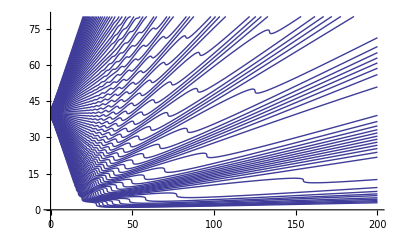

```mathematica
Plot[y[t]/.Hollandtabl5,{t,0,200}, PlotRange->{Full,{-5,80}}]
```

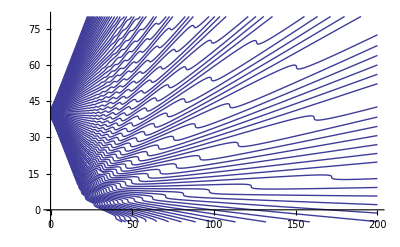

```mathematica
Plot[y[t]/.Hollandtabl7,{t,0,200}, PlotRange->{Full,{-5,80}}]
```

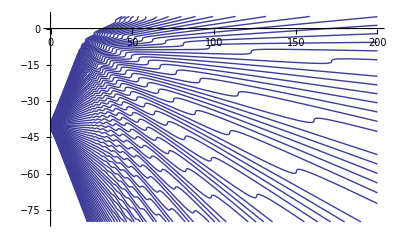

```mathematica
Plot[y[t]/.Hollandtabl7alt,{t,0,200}, PlotRange->{Full,{-80,5}}]
```

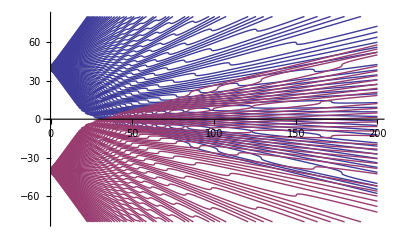

```mathematica
Plot[{y[t]/.Hollandtabl7,y[t]/.Hollandtabl7alt},{t,0,200}, PlotRange->{Full,{-80,80}}]
```

```mathematica
Hollandtabl6=NDSolve[{ⅈ D[y[x,t],t]== 1 D[D[y[x,t],x],x]+ 0.25 Abs[y[x,t]]^2 ,y[x,0]==(ⅇ^(-(5-x)^2/4)+ⅇ^(-(5+x)^2/4))/(2^(3/4) π^(1/4) √(1+ⅇ^(-5^2/2))),y[-100,t]==0,y[100,t]==0},y,{t,0,30},{x,-100,100}]
```

{{y→InterpolatingFunction[{{-100.,100.},{0.,30.}},<>]}}

```mathematica
Manipulate[Plot[Abs[y[x,t]/.Hollandtabl6]^2,{x,-100,100}, PlotRange->{Full,{0,0.1}}],{t,0,30}]
```

ReplaceAll::reps: {Hollandtabl6} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
datas = Table[{t,N[(1/2 ⅇ^(y/(1+0.15 t^2)) t (-100+y)+1/2 ⅇ^(-y/(1+0.15 t^2)) t (100+y)+t y Cos[(t y)/(1+0.15 t^2)]-Sin[(t y)/(1+0.15 t^2)])/((1+0.15 t^2) (ⅇ^(-y/(1+0.15 t^2))+ⅇ^(y/(1+0.15 t^2))+2 Cos[(t y)/(1+0.15 t^2)]))]},{t,0,30,0.05},{y,-200,200,0.4}];
```

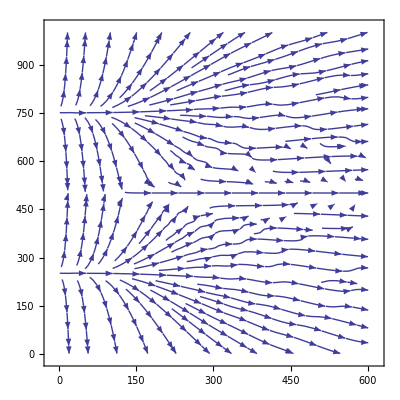

```mathematica
ListStreamPlot[datas]
```

```mathematica
FullSimplify[(1/(√(2 π) σ))ⅇ^(-(x-t)^2/(2 σ^2))]
```

(ⅇ^(-(t-x)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Integrate[ (ⅇ^(-(t-x)^2/(2 σ^2)))/(√(2 π) σ) ,{x,-∞,∞}]
```

1

```mathematica
Animate[Plot[(ⅇ^(-(t-x)^2/2))/(√(2 π)),{x,-10,10}, PlotRange->{Full,{0,0.5}}],{t,-10,10}]
```

```mathematica
anim = Table[Plot[(ⅇ^(-(t-x)^2/2))/(√(2 π)),{x,-10,10}, PlotRange->{Full,{0,0.5}}, PlotPoints->100,PlotStyle->Orange,Frame->True,FrameTicks->{False,False, False, False} ,Axes->False, Filling->Axis],{t,-10,10, 0.2}];
```

```mathematica
ListAnimate[anim]
```

```mathematica
Export["ClassicalGaussian.mov",anim]
```

ClassicalGaussian.mov